## Vacuum Oscillation Visualization

This notebook will explore the visualization of neutrino oscillations.

Neutrino Oscillations in Vacuum

```mathematica
sin2theta=Sin[2ArcSin[√0.302]]
```

0.918251

```mathematica
sin2theta^2
```

0.843184

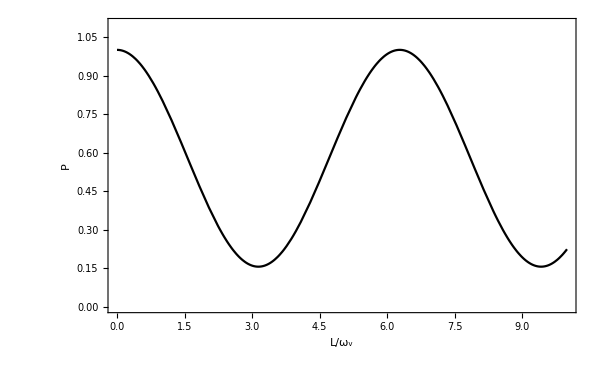

```mathematica
Plot[1-sin2theta^2*Sin[x/2]^2,{x,0,10},PlotRange->{Automatic,{0,1.1}},Frame->True,ImageSize->600,PlotStyle->Black,LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontWeight->"Bold",FontSize->18},FrameLabel->{"L/ω_v","P"}]
```